```mathematica
data = Import["~/Documents/home/writings/combined.txt"];
junk = {"comme", "quand","enfin","lorsque","après","jusqu","sinon","aujourd","autour","entre","aussi","toute","petit","avoir","encore","aurais","étais","avais","juste","leurs","parce"};
```

```mathematica
cleanedData = StringReplace[#, RegularExpression["\\b[0-9]+[/-][0-9]+([/-][0-9]+)?\\b"] -> ""] & /@ DeleteStopwords[ToLowerCase[TextWords[data]]];
cleanedData = Select[Flatten[StringSplit[StringReplace[cleanedData,PunctuationCharacter->" "]]],StringLength[#]>4 && #!="comme"&];
cleanedData = DeleteCases[cleanedData,x_/;MemberQ[junk,x]];
```

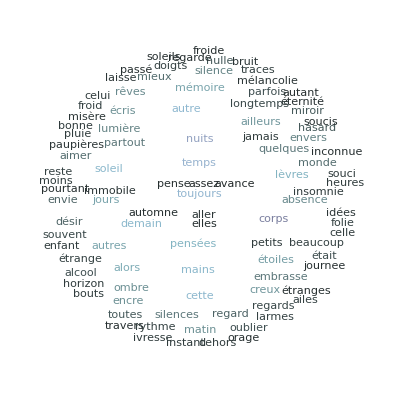

```mathematica
WordCloud[cleanedData, Disk[], ColorFunction->ColorData["AtlanticColors"]]
```